```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/rmtchem

## Regular random matrices

```mathematica
filebase="data/2_100_0";
Length[BinaryReadList[filebase<>".npy","Real64"][[17;;-1]]]^(1/2)
Length[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2]]^(1/2)
```

201

201

```mathematica
201*201
```

40401

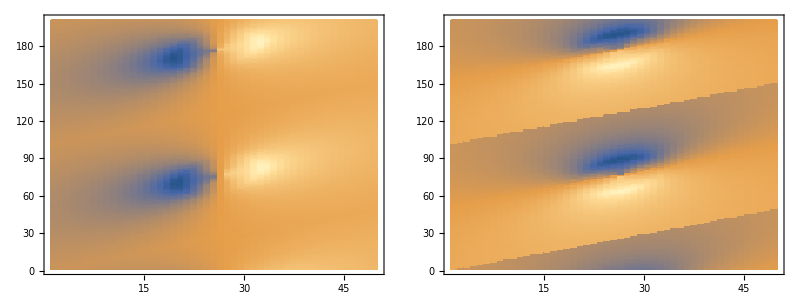

Part::partw: Part 52 of {{{{7.02021×10^-20+0.211442 ⅈ,-101.5-101.5 ⅈ},{-101.5+101.5 ⅈ,2.32697×10^-19+0.211442 ⅈ}},«49»,«151»},{«1»},«46»,{«1»},{{{1.44111×10^-18+0.504152 ⅈ,215.569+9.17375 ⅈ},«1»},«49»,«151»}} does not exist.

Part::partw: Part 53 of {{{{7.02021×10^-20+0.211442 ⅈ,-101.5-101.5 ⅈ},{-101.5+101.5 ⅈ,2.32697×10^-19+0.211442 ⅈ}},«49»,«151»},{«1»},«46»,{«1»},{{{1.44111×10^-18+0.504152 ⅈ,215.569+9.17375 ⅈ},«1»},«49»,«151»}} does not exist.

Part::partw: Part 54 of {{{{7.02021×10^-20+0.211442 ⅈ,-101.5-101.5 ⅈ},{-101.5+101.5 ⅈ,2.32697×10^-19+0.211442 ⅈ}},«49»,«151»},{«1»},«46»,{«1»},{{{1.44111×10^-18+0.504152 ⅈ,215.569+9.17375 ⅈ},«1»},«49»,«151»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
filebase="data/2_100_0";
n=Length[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2]]^(1/2);
gvals=Partition[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2],n];Grid[{{ListDensityPlot[Transpose[Re[gvals[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0],
ListDensityPlot[Transpose[Im[gvals[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0]}}]
gr=Interpolation[Flatten[Table[{-2+4/(n-1)*(i-1),-2+4/(n-1)*(j-1),Re[gvals[[i,j,2,1]]]},{j,Complement[Range[n],{(n-1)/2+1}]},{i,Complement[Range[n],{(n-1)/2+1}]}],1]]
gi=Interpolation[Flatten[Table[{-2+4/(n-1)*(i-1),-2+4/(n-1)*(j-1),Im[gvals[[i,j,2,1]]]},{j,Complement[Range[n],{(n-1)/2+1}]},{i,Complement[Range[n],{(n-1)/2+1}]}],1]]

c2=Partition[BinaryReadList[filebase<>".npy","Real64"][[17;;-1]],n];
Grid[{{ListDensityPlot[Join[Transpose[c2][[1;;(n-1)/2]],Transpose[c2][[(n-1)/2+2;;n]]],ImageSize->300,InterpolationOrder->0,PlotRange->All],ListDensityPlot[Flatten[Table[{x,y,(Derivative[1,0][gr][x,y]-Derivative[0,1][gi][x,y])/(2*Pi)},{x,-2,2,4/n},{y,-2,2,4/n}],1],ImageSize->300,PlotRange->All]}}]
ListPlot[{Transpose[{2*Range[(n-1)/2]/((n-1)/2),Transpose[c2][[(n-1)/2+2;;n,(n-1)/2+1]]}],Table[{Y,Evaluate[D[gr[x,y],x]-D[gi[x,y],y]]/(2*Pi)}/.{x->0,y->Y},{Y,0.1,5,0.1}]},ImageSize->300,InterpolationOrder->0,PlotRange->All,Axes->False,Frame->True,FrameLabel->{y,ρ},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]]
```

```mathematica
ListPlot[Table[{Y,Evaluate[D[gr[x,y],x]-D[gi[x,y],y]]}/.{x->0,y->Y},{Y,0,5,0.1}]]
```

data/test

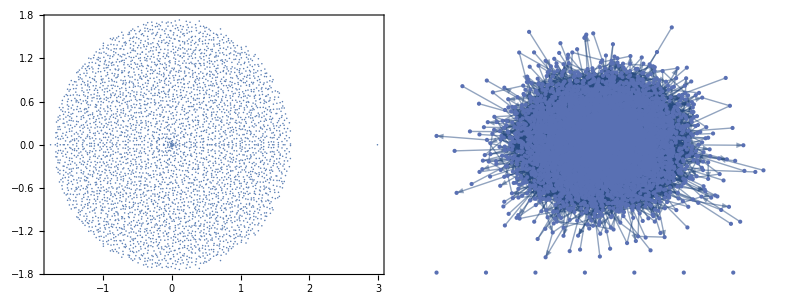

{0,10}

{0,11}

```mathematica
filebase="data/test"
mat=BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]];
n=Length[mat]^(1/2);
mat=Partition[mat,n];
evals=Partition[BinaryReadList[filebase<>"evals.npy","Real64"][[17;;-1]],2];
Grid[{{ListPlot[evals,ImageSize->300,AspectRatio->1,Axes->False,Frame->True,LabelStyle->Directive[16]],GraphPlot[AdjacencyGraph[mat/.u_/;Abs[u]>0->1/.(0.)->0],ImageSize->300]}}]
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@mat)
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@Transpose[mat])
```

```mathematica
Length[Length/@components]
```

571

{563.673,Null}

-Graphics-

stack.png

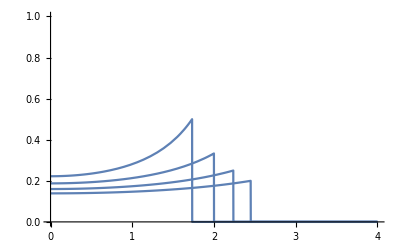

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];
c3=BinaryReadList["data/3.npy","Real64"][[17;;-1]];
c3=Transpose[Partition[c3,Length[c3]^(1/2)]];
c4=BinaryReadList["data/4.npy","Real64"][[17;;-1]];
c4=Transpose[Partition[c4,Length[c4]^(1/2)]];
c5=BinaryReadList["data/5.npy","Real64"][[17;;-1]];
c5=Transpose[Partition[c5,Length[c5]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;
AbsoluteTiming[{raster2,raster3,raster4,raster5}={Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c3[[1;;Floor[Length[c3]/2]]],c3[[Floor[Length[c3]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c4[[1;;Floor[Length[c4]/2]]],c4[[Floor[Length[c4]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c5[[1;;Floor[Length[c5]/2]]],c5[[Floor[Length[c5]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]};]
p=Rasterize[Plot3D[{0,2,4,6},{x,-10,10},{y,-10,10},Mesh->None,PlotRange->{{-8,8},{-8,8},{0,6}},PlotStyle->{Directive[Texture[raster2]],Directive[Texture[raster3]],Directive[Texture[raster4]],Directive[Texture[raster5]]},Lighting->{"Ambient",White},Boxed->False,Axes->False,Background->None,ImageSize->300,ViewPoint->{-12,0,2},AspectRatio->2,ViewAngle->0.065],ImageResolution->300];
Rotate[p,-Pi/2]
Export["stack.png",Rotate[p,-Pi/2]]
```

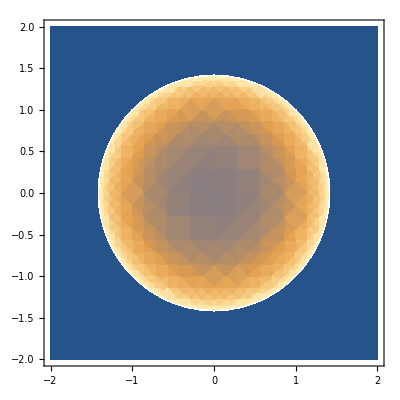

```mathematica
c=2;
DensityPlot[If[x^2+y^2<c,(c-1)*(c/(c^2-(x^2+y^2)))^2,0],{x,-c,c},{y,-c,c},PlotRange->All]
```

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;

p=Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],{c2[[Floor[Length[c2]/2]]]+c2[[2+Floor[Length[c2]/2]]]}/2,c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->{{100,400},{100,400}},Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]
Export["spectrum.png",p]
```

-Graphics-

spectrum.png

## Chemical reaction networks

data/test

{100,500}

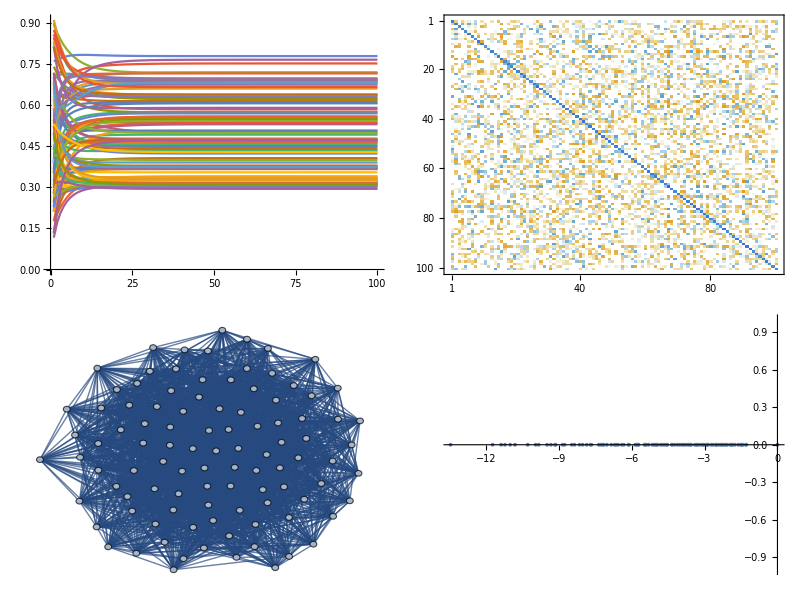

```mathematica
filebase="data/test"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

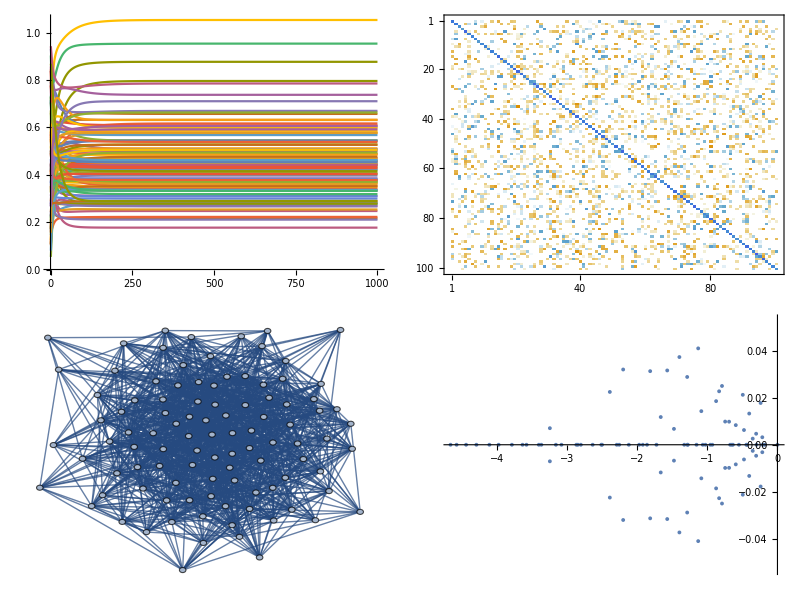

graph2.pdf

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
Export["graph2.pdf",AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300]]
```

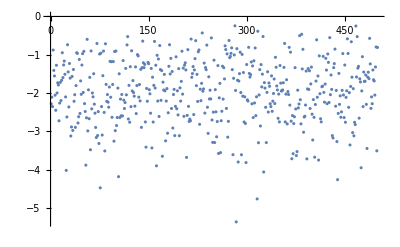

```mathematica
ListPlot[Diagonal[mat]]
```

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

-Graphics-